```mathematica
DominantWeights[highestweight_,cartanmatrix_] := Module[{cbhighestweight,cbdomweights},
cbhighestweight=Inverse[cartanmatrix].highestweight;
cbdomweights=Flatten[Table[{w1,w2},{w1,cbhighestweight[[1]],0,-1},{w2,cbhighestweight[[2]],0,-1}],1];
Return[DeleteCases[Transpose[cartanmatrix.Transpose[cbdomweights]], (x_ /;Min[x[[1]],x[[2]]]<0)]];
];

DominantWeights2[highestweight_,cartanmatrix_]:=Module[{domweights={},simpleroots},
(*Might be transpose of cartan*)
simpleroots=cartanmatrix.IdentityMatrix[Length[highestweight]];
SetAttributes[DWHelper,HoldFirst];
DWHelper[domweights,highestweight,simpleroots];
Return[domweights];
];
DWHelper[domweights_,weight_,simpleroots_]:=Module[{},
If[!MemberQ[domweights,weight]&&Min[weight]>=0,
domweights=Append[domweights,weight];
Table[DWHelper[domweights,weight-x,simpleroots],{x,simpleroots}];
];
];

Irrep[highestweight_] := Module[{minw, maxw, hexagonshells,triangleshells},
minw=Min[highestweight];
maxw=Max[highestweight];
hexagonshells = Table[ShellWeights[highestweight-i,i+1], {i,0,minw-1}];
triangleshells = Table[ShellWeights[Max[#,0]&/@(highestweight-i),minw+1], {i,minw,maxw,3}];
Return [Join[hexagonshells,triangleshells]];
];

(*Function which takes a 'corner' of a hexagon/triangle and produces all the weights in the hexagon/triangle
All weights are in the basis of the fundamental dominant weights
The roots are in the basis of the simple roots *)
ShellWeights[dominantweight_, dim_]:=Module[{weights,nextweight},
(*First deal with trivial rep*)
If[dominantweight=={0,0},
Return[Dataset[{<|"weight"->{0,0},"dim"->dim|>}]];
];

weights={<|"weight"->dominantweight,"dim"->dim|>};
(*Gets edge in alpha direction (top of hexagon)*)
weights = Join[weights,Edge[dominantweight,dim,{1,0}]];
nextweight=Last[weights]["weight"];
(*Gets edge in alpha+beta direction, etc.*)
weights=Join[weights,Edge[nextweight,dim,{1,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{0,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{1,0}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{1,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{0,1}]];

Return[Dataset[Drop[weights,-1]]];
];

(*Takes extremal weight of sl_2 module corresponding to root, gets all weights from that rep*)
Edge[weight_, dim_,root_]:=Module[{n,cartanmatrix},
n=Dot[weight,root];
(*Used to change basis from simple roots to fundamental dominant weight*)
cartanmatrix={{2,-1},{-1,2}};
Return[If[n<0,
Table[<|"weight"->(weight+x*(cartanmatrix.root)),"dim"->dim|>,{x,1,-n}],
Table[<|"weight"->(weight-x*(cartanmatrix.root)),"dim"->dim|>,{x,1,n}]]];
];

PlotIrrep[shells_]:=Module[{},
Return[Show[PlotWeights[#]&/@shells]];
];

(*Plots a given collection of weights in Euclidean coordinates*)
PlotWeights[weights_]:=Module[{cobmatrix},
cobmatrix={{Sqrt[3]/2,0},{1/2,1}};
Return[
ListPlot[Transpose[cobmatrix.Transpose[Normal[weights[All,"weight"]]]],
PlotStyle->PointSize[#]&/@(Normal[weights[All,"dim"]]*0.01)]
];
];
```

```mathematica
(*Examples*)
```

```mathematica
cartanmatrix={{2,-1},{-1,2}};
```

```mathematica
DominantWeights[{10,5},cartanmatrix]
```

{{10,5},{11,3},{12,1},{8,6},{9,4},{10,2},{11,0},{6,7},{7,5},{8,3},{9,1},{4,8},{5,6},{6,4},{7,2},{8,0},{2,9},{3,7},{4,5},{5,3},{6,1},{0,10},{1,8},{2,6},{3,4},{4,2},{5,0},{0,7},{1,5},{2,3},{3,1},{0,4},{1,2},{2,0},{0,1}}

```mathematica
DominantWeights2[{10,5},cartanmatrix]
```

{{10,5},{8,6},{6,7},{4,8},{2,9},{0,10},{1,8},{2,6},{0,7},{1,5},{2,3},{0,4},{1,2},{2,0},{0,1},{3,1},{3,4},{4,2},{5,0},{3,7},{4,5},{5,3},{6,1},{5,6},{6,4},{7,2},{8,0},{7,5},{8,3},{9,1},{9,4},{10,2},{11,0},{11,3},{12,1}}

```mathematica
(*Defining Rep*)
defRep=Irrep[{1,0}]
```

{Dataset[<>]}

```mathematica
(*Ad Rep Outer Shell*)
adRep=Irrep[{1,1}]
```

{Dataset[<>],Dataset[<>]}

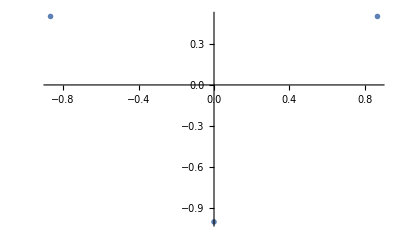

```mathematica
PlotIrrep[defRep]
```

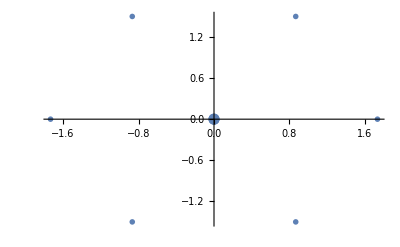

```mathematica
PlotIrrep[adRep]
```

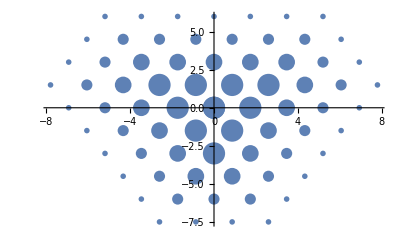

```mathematica
PlotIrrep[Irrep[{6,3}]]
```